## Background

```mathematica
coord={t,r,θ,ϕ};
dim=Length[coord];
Λ=1+1/4 B^2 r^2 Sin[θ]^2;
Δ=r (r-2 M);
gij={{Λ^2 Δ/r^2,0,0,0},{0,-(Λ^2 r^2)/Δ,0,0},{0,0,-Λ^2 r^2,0},{0,0,0,-(r^2 Sin[θ]^2)/Λ^2}};
gIJ=Inverse[gij]//Simplify;
g=Det[gij]//Simplify;
ΓIkl=Table[Sum[1/2 gIJ[[i,m]] (D[gij[[m,k]], coord[[l]]]+D[gij[[l,m]], coord[[k]]]-D[gij[[k,l]], coord[[m]]]),{m,dim}],{i,dim},{k,dim},{l,dim}]//Simplify;
Ai={0,0,0,-(B r^2 Sin[θ]^2)/(2Λ)};
Fij=Table[D[Ai[[j]], coord[[i]]]-D[Ai[[i]], coord[[j]]],{i,dim},{j,dim}]//Simplify;
FIJ=Table[Sum[gIJ[[i,k]]*gIJ[[j,l]]*Fij[[k,l]],{k,dim},{l,dim}],{i,dim},{j,dim}]//Simplify;
```

## Particle motion

```mathematica
a={t->T[τ],r->R[τ],θ->Θ[τ],ϕ->Φ[τ]};
xI={T[τ],R[τ],Θ[τ],Φ[τ]};
X={T,R,Θ,Φ};
uI=Table[D[xI[[i]],τ],{i,dim}];
ui=Table[Sum[gij[[i,j]]*uI[[j]]/.a,{j,dim}],{i,dim}]//Simplify;
```

```mathematica
eq=Table[D[xI[[i]],{τ,2}]+Sum[ΓIkl[[i,k,l]]*uI[[k]]*uI[[l]],{k,dim},{l,dim}]==α Sum[FIJ[[i,j]]*ui[[j]],{j,dim}]/.a,{i,dim}]//Simplify;
```

```mathematica
SolveValues[((Sum[uI[[i]]*ui[[i]],{i,dim}]//Simplify)/.{T'[τ]^2->x})==1,x]//Simplify
```

{(R[τ] (16+(R[τ] (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 R'[τ]^2)/(-2 M+R[τ])+R[τ]^2 (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 Θ'[τ]^2+(256 R[τ]^2 Sin[Θ[τ]]^2 Φ'[τ]^2)/((4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)))/((-2 M+R[τ]) (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)}

```mathematica
eq=Simplify[eq/.{T'[τ]->Sqrt[(R[τ] (16+(R[τ] (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 R'[τ]^2)/(-2 M+R[τ])+R[τ]^2 (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 Θ'[τ]^2+(256 R[τ]^2 Sin[Θ[τ]]^2 Φ'[τ]^2)/((4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)))/((-2 M+R[τ]) (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)]}];
```

```mathematica
eq=Solve[eq,{T''[τ],R''[τ],Θ''[τ],Φ''[τ]}][[1]]/.Rule->Equal;
```

```mathematica
s=NDSolve[Join[eq[[2;;]]/.{B->1,α->100,M->1},{R[0]==10,Θ[0]==Pi/10,Φ[0]==0,R'[0]==0,Θ'[0]==0,Φ'[0]==0}],X[[2;;]],{τ,0,10000}];
s1=NDSolve[{T'[τ]==Sqrt[(R[τ] (16+(R[τ] (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 R'[τ]^2)/(-2 M+R[τ])+R[τ]^2 (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 Θ'[τ]^2+(256 R[τ]^2 Sin[Θ[τ]]^2 Φ'[τ]^2)/((4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)))/((-2 M+R[τ]) (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)],T[0]==0}/.{B->1,M->1}/.s,T,{τ,0,10000}];
s=Flatten[Join[s1,s]]
```

{T→InterpolatingFunction[…],R→InterpolatingFunction[{{0., 10000.}}, <>],Θ→InterpolatingFunction[{{0., 10000.}}, <>],Φ→InterpolatingFunction[{{0., 10000.}}, <>]}

```mathematica
ParametricPlot3D[Evaluate[{R[τ]Sin[Θ[τ]]Cos[Φ[τ]],R[τ]Sin[Θ[τ]]Sin[Φ[τ]],R[τ]Cos[Θ[τ]]}]/.s,{τ,0,10000},PlotRange->{{-10,10},{-10,10},{-10,10}},PerformanceGoal->"Quality"]
```

-Graphics3D-

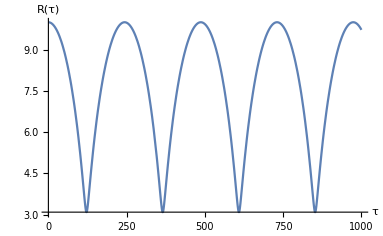

```mathematica
Plot[Evaluate[R[τ]]/.s,{τ,0,1000}, AxesLabel->{"τ","R(τ)"}]
```

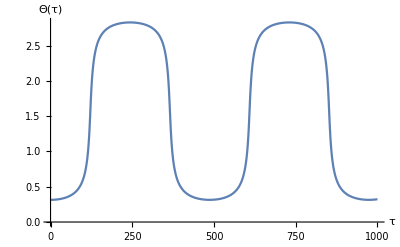

```mathematica
Plot[Evaluate[Θ[τ]]/.s,{τ,0,1000}, AxesLabel->{"τ","Θ(τ)"}]
```

```mathematica
ParametricPlot[{Evaluate[T[τ]],Evaluate[R[τ]]}/.s,{τ,0,1000}, AxesLabel->{"t","R(t)"},PlotRange->Automatic,AspectRatio->1/2]
```

```mathematica
s1=NDSolve[{T'[τ]==Sqrt[(R[τ] (16+(R[τ] (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 R'[τ]^2)/(-2 M+R[τ])+R[τ]^2 (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2 Θ'[τ]^2+(256 R[τ]^2 Sin[Θ[τ]]^2 Φ'[τ]^2)/((4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)))/((-2 M+R[τ]) (4+B^2 R[τ]^2 Sin[Θ[τ]]^2)^2)],T[0]==0}/.{B->1,M->1}/.s,T,{τ,0,153}]
```

{{T→InterpolatingFunction[…]}}

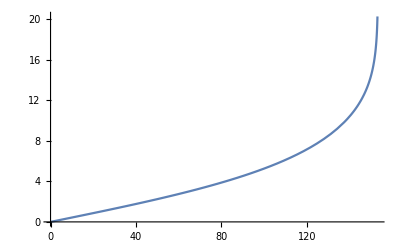

```mathematica
Plot[Evaluate[T[τ]]/.s1,{τ,0,153}]
```

## Field

```mathematica
σ[x_,z_,param_]:=Module[{eq,s},eq=Table[D[xI[[i]],{τ,2}]==-Sum[ΓIkl[[i,k,l]]*uI[[k]]*uI[[l]],{k,dim},{l,dim}],{i,dim}]/.a;s=NDSolve[Join[eq,Thread[{T[0],R[0],Θ[0],Φ[0]}==x],Thread[{T[1],R[1],Θ[1],Φ[1]}==z]]/.param,{T,R,Θ,Φ},{τ,0,1},PrecisionGoal->7];1/2 NIntegrate[Sum[gij[[i,j]]*uI[[i]]*uI[[j]],{i,dim},{j,dim}]/.a/.param/.s,{τ,0,1}][[1]]]
```